# Analysis of Execution Times of the Brute Force and “Smart” Segment Intersection Algorithms

## July 2023

## 1. Read the Data Files and Organize the Data

### 1.1 Read the Files

So far, all paths are hard-coded

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../DataFiles"];
FileNames[]
```

{bruteResults.txt,data1.txt,data2.txt,smartResults.txt}

```mathematica
bruteData=ReadList["bruteResults.txt",{Number,Number,Number}];
smartData=ReadList["smartResults.txt",{Number,Number,Number}];
```

### 1.2 Group the lists of 2D points

The data are triplets {number of segments, number of intersections found, execution time}.
I am regrouping them into two pairs
     {number of segments, execution time}
     {number of intersections found, execution time}

#### 1.2.1 Segments and time

```mathematica
bruteSegTime=Transpose[Delete[Transpose[bruteData],2]];
smartSegTime=Transpose[Delete[Transpose[smartData],2]];
```

#### 1.2.2 Intersections and time

```mathematica
bruteIntersectTime=Transpose[Delete[Transpose[bruteData],1]];
smartIntersectTime=Transpose[Delete[Transpose[smartData],1]];
```

#### 1.2.3 Time ratios

```mathematica
segTimeRatio=Table[{bruteData[[k]][[1]],N[smartData[[k]][[3]]/bruteData[[k]][[3]]]},{k,1,Dimensions[bruteData][[1]]}];
intersectTimeRatio=Table[{bruteData[[k]][[2]],N[smartData[[k]][[3]]/bruteData[[k]][[3]]]},{k,1,Dimensions[bruteData][[1]]}];
```

## 2. Now Do Some Plotting

### 2.1 Direct plotting, no processing

#### 2.1.1 Together [awful]

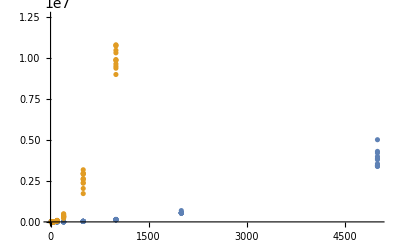

```mathematica
ListPlot[{bruteSegTime,smartSegTime}]
```

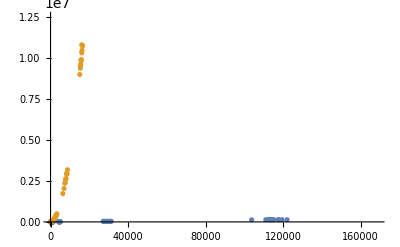

```mathematica
ListPlot[{bruteIntersectTime,smartIntersectTime}]
```

#### 2.1.2 Only brute force

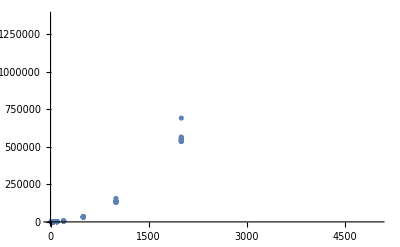

```mathematica
ListPlot[bruteSegTime]
```

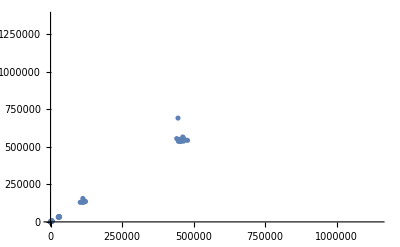

```mathematica
ListPlot[bruteIntersectTime]
```

#### 2.1.2 Only “smart” force

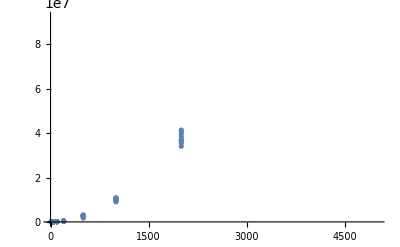

```mathematica
ListPlot[smartSegTime]
```

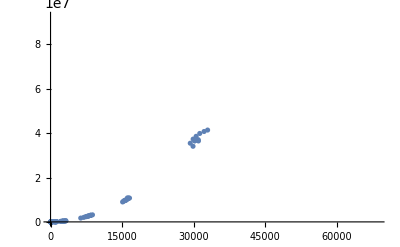

```mathematica
ListPlot[smartIntersectTime]
```

### 2.2 Polynomial fit

21527.4-170.856 x+0.232193 x^2

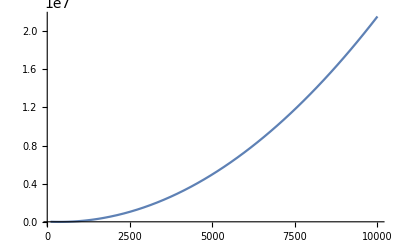

```mathematica
bruteSegQuadFit[x_]=Fit[bruteSegTime,{1,x,x^2},x];
bruteSegQuadFit[x]
Plot[bruteSegQuadFit[x],{x,100,10000}]
```

2.89749×10^6-25383.4 x+27.2086 x^2

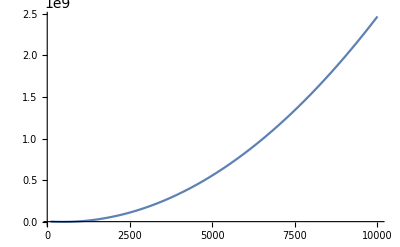

```mathematica
smartSegQuadFit[x_]=Fit[smartSegTime,{1,x,x^2},x];
smartSegQuadFit[x]
Plot[smartSegQuadFit[x],{x,100,10000}]
```

117148.-1300.63 x+9.00076 x^2+0.00270565 x^3

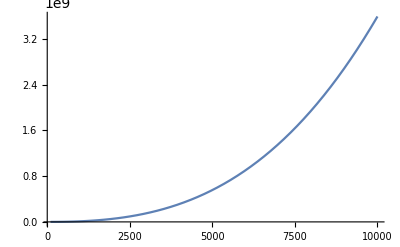

```mathematica
smartSegCubicFit[x_]=Fit[smartSegTime,{1,x,x^2,x^3},x];
smartSegCubicFit[x]
Plot[smartSegCubicFit[x],{x,100,10000}]
```

5707.22+1.03049 x+2.39426×10^-7 x^2

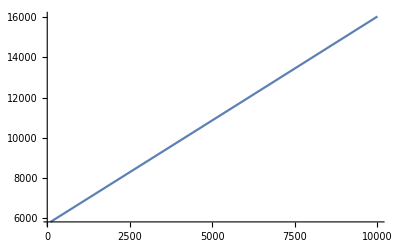

```mathematica
bruteIntersectQuadFit[x_]=Fit[bruteIntersectTime,{1,x,x^2},x];
bruteIntersectQuadFit[x]
Plot[bruteIntersectQuadFit[x],{x,100,10000}]
```

6.12789×10^7-1.19002×10^7 √x+423993. x-4918.99 x^(3/2)+19.1147 x^2-0.0000848547 x^3

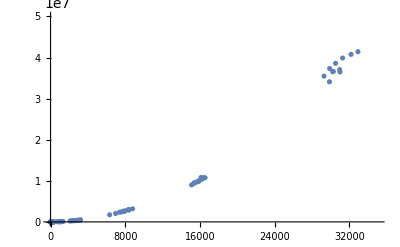

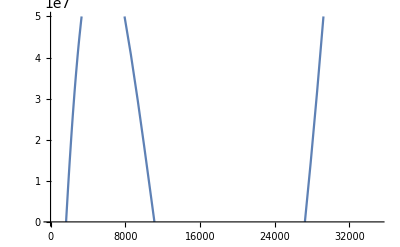

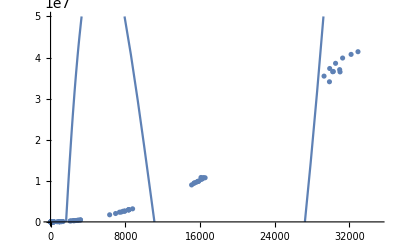

```mathematica
smartIntersectQuadFit[x_]=Fit[smartIntersectTime,{1,√x,x,x √x,x^2,x^3},x];
smartIntersectQuadFit[x]
smartPlot1=ListPlot[smartIntersectTime,PlotRange->{{0,35000},{0,5*10^7}}]
smartPlot2=Plot[smartIntersectQuadFit[x],{x,100,35000},PlotRange->{{0,35000},{0,5*10^7}}]
Show[{smartPlot1,smartPlot2}]
```

### 2.3 Ratios

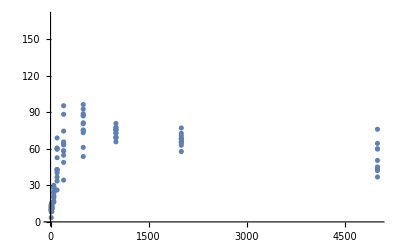

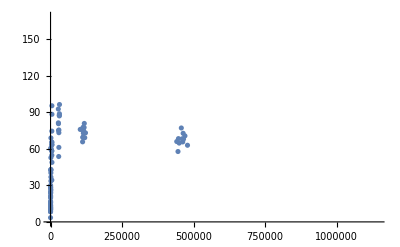

```mathematica
ListPlot[segTimeRatio]
ListPlot[intersectTimeRatio]
```